# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Lecture 06 — Wednesday October 07, 2020

## Additional Topics in Options Theory The Black-Scholes Pricing Formula Mathematica’s FinancialDerivative[] Function Numerical Methods Implied Volatility

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## A Simple Stock Model

We can apply the above to model constant coefficient geometric Brownian motion of a stock price S(t)

ⅆS(t) = μ S(t) ⅆt + σ S(t) ⅆW(t)

Sometimes this is expressed in terms of the instantaneous rate of return of the stock. Dividing both sides by S(t)

(ⅆS(t))/(S(t))=μ ⅆt+σⅆW(t)

Note that our earlier experiments with the geometric binomial lattice (which in the limit is the same at the price model above) it appeared that the log price was Normally distributed. Let S follow the constant-coefficient geometric process above with S(0) = 1. Take g[S(t), t] = log S(t) and apply Itô’s lemma then we get

```mathematica
xIto[a_Function,b_Function,g_Function,s_Symbol,t_Symbol]:={a[s,t]D[g[s,t], s]+D[g[s,t], t]+1/2 b[s,t]^2 D[g[s,t], s,s],b[s,t]D[g[s,t], s]}
```

```mathematica
xIto[Function[{s,t},s μ],Function[{s,t},s σ],Function[{s,t},Log[s]],s,t]
```

{μ-σ^2/2,σ}

You can also specify the function arguments using “&” notation.

```mathematica
xIto[μ #&,σ #&,Log[#]&,s,t]
```

{μ-σ^2/2,σ}

Thus, we have

ⅆ log S(t)=(μ-1/2 σ^2)ⅆt+σ ⅆW(t)

Thus, log S(t) is Normally distributed with a mean of  (μ-1/2 σ^2) t and a standard deviation of σ√t. It is also clear that S(t) is log Normally distributed and

log S(t)=(μ-1/2 σ^2)t+σ W(t)    ⟹    S(t)=S(0)ⅇ^((μ-1/2 σ^2)t+σ W(t))

## Put-Call Parity for European Options

At time t ≤ T for options on the same underlying S at a given strike price K and expiry T, put-call parity for European options in an arbitrage-free market is

S(t)=C(t)-P(t)+K ⅇ^(-r(T-t))

Consider the individual components at expiry. The following equally must hold:

S(T)=Max[S(T)-K,0]-Max[K-S(T),0]+K

A plot of the positions at expiry clearly indicate this

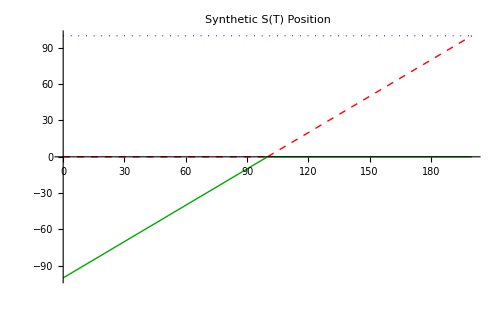

To see why put-call parity holds at time t≤T, assume that the market is arbitrage-free but that put-call parity is violated. This leaves us with two mutually exclusive alternatives:

S(t)<C(t)-P(t)+K ⅇ^(-r(T-t)) — The stock is undervalued or equivalently the options-plus-cash position is overvalued.  Therefore, one side of the trade is (buy the stock) and the other is (sell the call, buy the put, borrow cash). The cashflow of this trade at time t is -S(t)+C(t)-P(t)+K ⅇ^(-r(T-t))>0 resulting in an immediate positive cashflow. The trade is held until expiry and closed with a net zero cashflow at that time. Thus, an immediate riskless profit of -S(t)+C(t)-P(t)+K ⅇ^(-r(T-t)) is realized at time t.

S(t)>C(t)-P(t)+K ⅇ^(-r(T-t)) — The stock is overvalued or equivalently the options-plus-cash position is undervalued. Therefore, one side of the trade is (sell short the stock) and the other is (buy the call, sell the put, deposit cash). The cashflow of this trade at time t is S(t)-C(t)+P(t)-K ⅇ^(-r(T-t))>0 resulting in an immediate positive cashflow. The trade is held until expiry and closed with a net zero cashflow at that time. Thus, an immediate riskless profit of S(t)-C(t)+P(t)-K ⅇ^(-r(T-t)) is realized at time t.

Thus, the violation of put-call parity contradicts the arbitrage-free assumption. Note that in an arbitrage one buys the undervalued position and sells the overvalued one.

## The Black-Scholes PDE

### Forming Risk Free Portfolios

Consider the simplest realistic model of price dynamics, a geometric, constant coefficient SDE,

ⅆS(t)=μ S(t) ⅆt+σ S(t) ⅆW(t)

If we have a derivative whose price F(S(t), t) is a function of the underlying and time, then the dynamics of the derivative are driven by

ⅆF(t)=((∂F)/(∂S)μ S(t)+(∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2))ⅆt+(∂F)/(∂S)σ S(t)ⅆW(t)

Now we wish to consider a portfolio

Π(t)=F(t)-ϑ_S(t)S(t)

which is composed of buying one unit of the derivative and selling ϑ_S(t) units of the underlying so that

ⅆΠ(t)=ⅆF(t)-ϑ_S(t)ⅆS(t)

Next substitute the RHS of the equation for ⅆF(t) into that of ⅆΠ(t)

ⅆΠ(t)=[((∂F)/(∂S)-ϑ_S(t))μ S(t)+(∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2)]ⅆt+((∂F)/(∂S)-ϑ_S(t))σ S(t)ⅆW(t)

If we now maintain  ϑ_S(t)=∂F/∂S over an infinitesimal interval ⅆt, then the term ((∂F)/(∂S)-ϑ_S(t)) associated with ⅆW(t) disappears leaving

ⅆΠ(t)=((∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2))ⅆt

and we have eliminated randomness from the portfolio. Note that because we can think of the function ϑ_S(t) as being held constant in a infinitesimal interval we do not have to include a term for ⅆϑ_S(t).

The Portfolio Π(t) is often called the replicating portfolio.

### Interpreting the Replicating Portfolio

The function ϑ_S(t)is called the hedge ratio and the technique above is called delta hedging. If we assume that we can maintain the hedge from instant to instant and that there are no liquidity limitations or transaction costs, then a arbitrage free market demands that the riskless portfolio Π(t) returns the risk-free rate. This suggests another condition on Π(t)

ⅆΠ(t)=r Π(t)ⅆt

where r is the risk free rate and the LHS is the differential equation representing a continuously compounded return.

If we consider the case of geometric constant coefficient SDE and the equation above

r Π(t)ⅆt=((∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2))ⅆt

Substituting with ∂F/∂S substituted for ϑ_S(t) in the original expression for Π(t) above we have

r (F(t)-(∂F)/(∂S)S(t))ⅆt=((∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2))ⅆt

Dividing through by ⅆt and rearranging terms yields

(∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2)+r S(t)(∂F)/(∂S)-r F(t)=0

The is the Black-Scholes PDE (a parabolic PDE) and is a form of the heat equation. It plays a major role in the pricing of derivatives.

## Black-Scholes Formula

The Black-Scholes PDE is a parabolic PDE that is a form of the well known heat equation. The solution is beyond the scope of this class (however, interested readers can consult http://en.wikipedia.org/wiki/Black-Scholes_equation). For the constant coefficient case the PDE has an analytical solution. In its more general forms it may need to be solved numerically using either Monte Carlo or finite difference methods.

### European Call

The analytical solution is for constant coefficient geometric Brownian motion is

C(S(t),t)=S(t)Φ(d_1)-K e^(-r(T-t))Φ(d_2)

where

d_1=(ln(S_t/K)+(r+1/2 σ^2)(T-t))/(σ √(T-t))

d_2=d_1-σ √(T-t)

and  Φ(d) is the cumulative standard Normal distribution

Φ(d)=∫_(-∞)^d 1/(√(2π))e^(-1/2 x^2)ⅆx

### European Put

P(t)=K e^(-t(T-t))Φ(-d_2)-S_t Φ(-d_1)

### Example — Option Valuation over Underlying Price and Time to Expiry

Consider a call option at time t = 0 with a strike price K = 100 and expiry T = 0.25 years. The riskfree rate is r = 6.5%. The underying asset is currently at the money at S_0 = 100 and has an annual volatility of σ = 30%. Then the current price of the option using the Black-Scholes formula is C(t) = 6.77098.

If we plot this option’s price over 0≤t≤T and 80≤S≤120, then we realize the surface

## Risk-Neutral Measure

### Without Dividends or Holding Costs

In order for the SDE to correctly model the dynamics of the asset, the effect of any cash-flows—either positive from dividends or negative from holding costs—must be reflected in the SDE describing the return. We will first consider the development of the risk-neutral measure when no such cash-flows are present. Under the normal measure P the return process is

(ⅆS(t))/(S(t))=μⅆt+σⅆW_P(t)

and the expected return is

E_P[(ⅆS(t))/(S(t))]=μ

We know that under the risk-neutral measure Q

S(t)=e^(-r(T-t))E_Q[S(T)]

Thus, we wish a change in measure

E_Q[(ⅆS(t))/(S(t))]=r

Rearranging the SDE

(ⅆS(t))/(S(t))=rⅆt+σ((μ-r)/σ ⅆt+ⅆW_P(t))

and selecting a measure Q such that

(μ-r)/σ ⅆt+ⅆW_P(t)=ⅆW_Q(t)

we have transformed the SDE into the risk-neutral form so that under the probability measure Q

(ⅆS(t))/(S(t))=rⅆt+σⅆW_Q(t)

E_Q[(ⅆS(t))/(S(t))]=rⅆt

S(t)=e^(-r(T-t))E_Q[S(T)]

Thus, the risk-neutral SDE now has the drift term r and original volatility term σ. Once we have the risk neutral measure, we can also compute the value of any derivative that depends upon the security, e.g.,

F(S(t),t)=e^(-r(T-t))E_Q[F(S(T),T)]

We will use this relationship shortly to show how an option price can be estimated using Monte Carlo simulation.

### Incorporating Storage Costs

Consider an asset S whose price follows a constant coefficient geometric Brownian motion and which has proportional holding costs paid at a rate of η per unit time. Let H designate the “net” asset of holding S but selling off enough of the position to fund the holding costs. This net asset follows the SDE with μ and σ the same as those of S:

(ⅆH(t))/(H(t))=μ ⅆt-η ⅆt+σⅆW_P(t)

If we are building a risk-neutral solution, then we must do so in terms of this net asset because this reflects the true value of the wealth of the position over time; hence, (μ-η)→r

(ⅆH(t))/(H(t))=r ⅆt+σⅆW_Q(t)

In terms of the original asset S  we have μ→r+η; therefore, the risk-neutral solution for the original asset has a drift term of r+η :

(ⅆS(t))/(S(t))=(r+η)ⅆt+σⅆW_Q(t)

### Incorporating Dividends

It should be obvious the if position returns dividends at proportional rate δ per unit time. Using the same approach above, then the risk-neutral SDE is

(ⅆS(t))/(S(t))=(r-δ)ⅆt+σⅆW_Q(t)

### Both Dividends and Holding Costs

(ⅆS(t))/(S(t))=(r+η-δ)ⅆt+σⅆW_Q(t)

## Dividends and Holding Costs with the Black-Scholes Solution

In the Black-Scholes solution accounting for dividends changes the value of the replicating portfolio by adding the dividend effect to the hedge:

ⅆΠ(t)=ⅆF(t)-ϑ_S(t)(ⅆS(t)+δ S(t)ⅆt)

The required delta hedge is still ϑ_S(t)=∂F/∂S. The hedged position with its random elements now removed is set to the risk-free portfolio. Note the additional term -δ S(t)∂F/∂S:

r Π(t)ⅆt=((∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2)-δ S(t)(∂F)/(∂S))ⅆt

After following through the computations, we have the revised PDF

(∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2)+(r-δ) S(t)(∂F)/(∂S)-r F(t)=0

The result for proportional holding costs η would by the same logic follow the same pattern but with its sign reversed:

(∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2)+(r+η) S(t)(∂F)/(∂S)-r F(t)=0

Thus, our result is the same as the risk-neutral approach above: r→r-δ+η for S(t) in the presence of proportional dividends and holding costs.

## Monte Carlo Integration

Under the risk-neutral measure Q the price dynamics replaces the actual mean with the risk-free mean and keeps the same volatility.

Consider the original example: a call option at time t = 0 with a strike price K = 100 and expiry T = 0.25 years. The risk free rate is r = 6.5%. The underlying asset is currently at the money at S(0) = 100 and has an annual volatility of σ = 30%. Recall that the current price of the option using the Black-Scholes formula is C_0 = 6.77098.

Under the risk-neutral measure the price dynamics are

S(t)=S(0) e^((r - σ^2/2)t + σ W(t))

where W(t)~N[0, √t].

To price a call option we can generate n random samples. Designate the kth such experiment S^(k)(T)=S(0)ⅇ^((r-σ^2/2)T+σ randN[0, √T]), where randN[0, √T] is a function that generates a random number with an N[0, √T] distribution. The Monte Carlo estimate for the integral is

C(S(0),0)=e^(-r T)E^Q[C(S(T),T)]≃e^(-r T)/n(∑_(k=1)^n max[S^(k)(T)-K, 0])

In this instance, we have an  analytical solution for S(T) for comparison. If this were not the case, then we could have proceeded directly from the SDE describing the asset dynamics under the risk neutral measure to simulate the trajectories S^(k)(T).

The approach of replacing the actual drift with the risk-free rate but preserving the original volatility structure is valid under a fairly large number of circumstances. For example, if the risk-free rate or volatility are themselves stochastic processes with their own SDEs, then such situations can be handled without undue complication.

As noted above, if there are proportional dividends δ and storage costs η per unit time, then the appropriate discounting uses the risk-neutral rate r-δ+η.

One problem of Monte Carlo techniques is the standard error of the estimate tends to be proportional to 1/√n, for a sample size of n. However, we have explored only the most simple sampling approach. There are a number of techniques available to increase the efficiency of Monte Carlo integration.

### Example I — European Call Option Pricing

Applying standard statistical methodology we can compute the standard deviation of the estimate by dividing the standard deviation of the sample by square root of the sample size. A simulation with  n = 1000 is demonstrated.

#### Code

The function below returns the estimated mean of the call price and the sampling error of the mean.

```mathematica
xEuroCallOptMonteCarlo[nNowPrice_,nVolatility_,nStrikePrice_,nExpiry_,nRiskFree_,iSamples_]:={Mean[#],StandardDeviation[#]/√iSamples}&[Exp[-nRiskFree nExpiry](Max[#-nStrikePrice,0]&/@(nNowPrice Exp[(nRiskFree-nVolatility^2/2.)nExpiry]Exp[ nVolatility RandomVariate[NormalDistribution[0,√nExpiry],iSamples]]))];
```

For example, an at-the-money put is estimated at

```mathematica
xEuroCallOptMonteCarlo[100.,0.3,100.,0.25,0.065,1000]
```

{6.89899,0.302564}

For comparison, the Black-Scholes solution is 6.77098.

### Example II — Plotting the Alternatives

We repeated this process for prices of 85 to 105. The results with ± 1.96 standard errors are plotted against the Black-Scholes results below.

#### Simulation of Estimates with their 95% Confidence Levels

```mathematica
mnSim=Transpose@Block[
{sol},
Table[
sol=xEuroCallOptMonteCarlo[price,0.3,100.,0.25,0.065,1000];
{{price,sol⟦1⟧-1.96sol⟦2⟧},{price,sol⟦1⟧},{price,sol⟦1⟧+1.96sol⟦2⟧}},
{price,85.,105.,5.}
]
]
```

{{{85.,1.02912},{90.,1.6618},{95.,4.06581},{100.,6.30954},{105.,9.32011}},{{85.,1.29675},{90.,1.9879},{95.,4.55989},{100.,6.94762},{105.,10.0496}},{{85.,1.56438},{90.,2.31399},{95.,5.05396},{100.,7.5857},{105.,10.779}}}

#### Plot Comparing Black-Scholes and the Monte Carlo Solutions

This example uses Mathematica’s FinancialDerivative[] function which uses Black-Scholes for pricing vanilla European options and will be described later in the class. A plot comparing the analytical Black-Scholes prices with the simulated prices and their 95% confidence intervals is

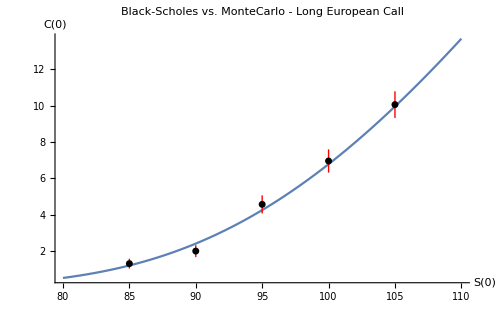

```mathematica
Show[
Plot[FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 100.00, "Expiration"->0.25},  {"InterestRate"-> 0.065, "Volatility" -> 0.3, "CurrentPrice"-> price}],{price,80,110},PlotLabel->Style["Black-Scholes vs. MonteCarlo - Long European Call",FontSize->16],AxesLabel->(Style[#,FontSize->14]&/@{"S(0)","C(0)"})],
ListPlot[mnSim,PlotStyle->{{PointSize[0]},{Black,PointSize[0.01]},{PointSize[0]}},Filling->{1->{3}},FillingStyle->Red],PlotRange->All,ImageSize->500
]
```

## The Finite Difference Method

A numerical method that is an alternative to Monte Carlo is the finite difference method (See http://en.wikipedia.org/wiki/Finite_Difference_Method). As we saw with the development of the Black-Scholes solution earlier, the result of an appropriate delta hedge is to remove randomness from the model, allowing us to reformulate the option pricing problem as a parabolic partial differentiable equation (PDE).

(∂F)/(∂t)+1/2 σ^2(S(t))^2(∂^2 F)/(∂S^2)+(r+η) S(t)(∂F)/(∂S)-r F(t)=0

Our purpose here is to give you some general insights into how the method works. For some option pricing problems, the resulting PDF cannot be solved analytically and a numerical technique, such as Monte Carlo integration or the finite difference method, must be used.

The finite difference method approximates differentials with discrete increments. Euler’s method is the simplest and most direct approach. Consider an approximation of the first derivative

(ⅆf(x))/ⅆx≃(f(x+Δ)-f(x))/Δ,    for Δ sufficiently small

Say we had an ordinary differential equation (ODE) f^′(x)=a+b f(x). Using the approximation f^′(x)≃(f(x+Δ)-f(x))/Δ and solving for f(x+Δ) yields the approximation:

f(x+Δ)≃f(x)+Δ(a+b f(x))

Consider the case a=1, b=2 with the initial condition f(0)=0.5. We can solve this in Mathematica using DSolve[] which gives the solution f(x)=ⅇ^(2x)-1/2:

```mathematica
DSolve[{f'[x]==1+2f[x],f[0.]==0.5},f,x]
```

{{f→Function[{x},1. (-0.5+1. ⅇ^(2 x))]}}

```mathematica
xSol=First[f/.DSolve[{f'[x]==1+2f[x],f[0.]==0.5},f,x]]
```

Function[{x},1. (-0.5+1. ⅇ^(2 x))]

Applying Euler’s method to approximate f(x) with Δ=0.01, we set up NestList[] to recursively compute {x, f(x)} beginning with {0., 0.5} for 0≤x≤2:

```mathematica
mnFiniteDiff=NestList[{First[#]+0.001,(Last[#]+0.001(1+2Last[#]))}&,{0.,0.5},2000];
```

A plot of the two solutions shows close agreement:

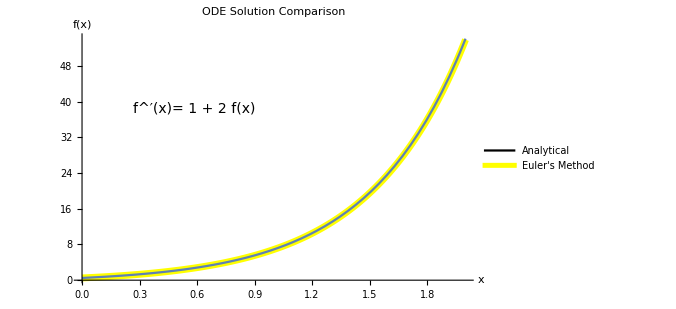

```mathematica
Show[
ListLinePlot[mnFiniteDiff,PlotStyle->{Thickness[0.01],Yellow},PlotStyle->Black,PlotLegends->LineLegend[{Black,{Thickness[0.01],Yellow}},{"Analytical","Euler's Method"}],PlotLabel->Style["ODE Solution Comparison",FontSize->16],AxesLabel->(Style[#,FontSize->14]&/@{"x","f(x)"})],
Plot[xSol[x],{x,0.,2.}],
Graphics[Text[Style["f^′(x)= 1 + 2 f(x)",FontSize->14],Scaled[{0.3,0.7}]]],
PlotRange->All,ImageSize->500
]
```

This approach can be extended to higher-order derivatives and systems of equations. There are also many approaches more effective than Euler’s method to approximating the derivatives. Although the example here appears straightforward, depending on the functions involved, there can be significant challenges in overcoming the numerical instabilities which arise.

## Mathematica’s FinancialDerivative[] Function

The FinancialDerivative[] function provides the solution for a wide range of options. The general form is

```mathematica
?FinancialDerivative
```

RowBox[{"FinancialDerivative", "[", RowBox[{StyleBox["instrument", "TI"], ",", StyleBox["params", "TI"], ",", StyleBox["ambientparams", "TI"]}], "]"}] gives the value of the specified financial instrument.
RowBox[{"FinancialDerivative", "[", RowBox[{StyleBox["instrument", "TI"], ",", StyleBox["params", "TI"], ",", StyleBox["ambientparams", "TI"], ",", StyleBox["prop", "TI"]}], "]"}] computes the specified property StyleBox["prop", "TI"].

FinancialDerivative[] handles a wide array of option types and to solve them will automatically deploy analytical, Monte Carlo or finite difference techniques as needed.

### Example — Vanilla European Options Pricing

For European options, e.g., a put and a call with strike K=150.00 and expiry T=0.5 for the underlying S(0)=153.25, σ=0.4, and rate r=0.02.

```mathematica
FinancialDerivative[{"European","Put"}, {"StrikePrice"-> 150.00, "Expiration"->0.5},  {"InterestRate"-> 0.02, "Volatility" -> 0.4, "CurrentPrice"->153.25}]
```

14.701

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 150.00, "Expiration"->0.5},  {"InterestRate"-> 0.02, "Volatility" -> 0.4, "CurrentPrice"->153.25}]
```

19.4435

### Example — Plots

We will use the same options above and underlying volatility but vary the underlying’s price. The valuations of the put and call, respectively, are:

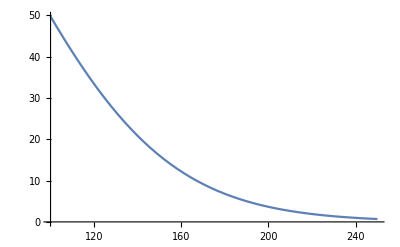

```mathematica
Plot[FinancialDerivative[{"European","Put"}, {"StrikePrice"-> 150.00, "Expiration"->0.5},  {"InterestRate"-> 0.02, "Volatility" -> 0.4, "CurrentPrice"->s}],{s,100,250},ImageSize->400]
```

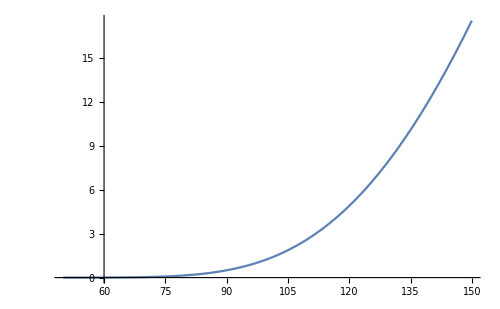

```mathematica
Plot[FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 150.00, "Expiration"->0.5},  {"InterestRate"-> 0.02, "Volatility" -> 0.4, "CurrentPrice"->s}],{s,50,150},ImageSize->500]
```

### Example — 3D Plots

We will use the same put option above and underlying volatility but vary the underlying’s price and the options expiry to produce the surface:

```mathematica
Plot3D[FinancialDerivative[{"European","Put"}, {"StrikePrice"-> 150.00, "Expiration"->t},  {"InterestRate"-> 0.02, "Volatility" -> 0.4, "CurrentPrice"->s}],{s,100,250},{t,0.,0.5},ImageSize->400]
```

-Graphics3D-

Another way to represent the same information is to overlay several 2D plots with varying expiries. The Tooltip[ ] function is used to label each plot line. The label is revealed when the mouse cursor touches the line.

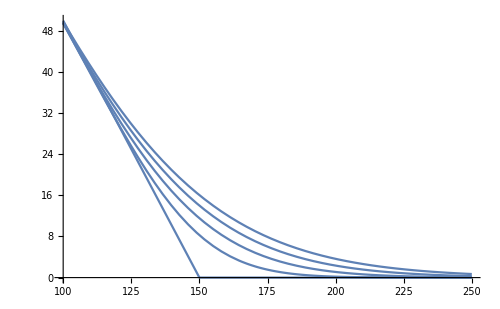

```mathematica
Show[
Table[
Plot[Tooltip[FinancialDerivative[{"European","Put"}, {"StrikePrice"-> 150.00, "Expiration"->x},  {"InterestRate"-> 0.02, "Volatility" -> 0.4, "CurrentPrice"->s}],x],{s,100,250},ImageSize->500],
{x,0.,0.5,0.125}
]
]
```

## Dividends and Holding Costs (Again)

We will start with a baseline example:

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 50.00, "Expiration"->1},  {"InterestRate"-> 0.1, "Volatility" -> 0.5, "CurrentPrice"->53.25}]
```

14.2258

We will only consider the case of continuous and fixed dividends. The necessary adjustments for holding costs are the same with the obvious sign reversal.

### Continuous Rate

If a stock returns dividends with a constant rate δ, then the Black-Scholes solution above must be adjusted to reflect the fact that the option holder does not receive the dividend payments. In the replicating portfolio we must hedge the option with the stock without its dividend income. Thus, we must replace the current price discounted for the expected future dividends, i.e., e^(-δ(T-t))S(t), into the original Black-Scholes formula. This will correctly account for this effect.

#### Example

Consider the example above. If the same stock paid a dividend at a constant annual rate of 4%, then the value of the call would fall from $14.23 to $12.76:

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 50.00, "Expiration"->1},  {"InterestRate"-> 0.1, "Volatility" -> 0.5, "CurrentPrice"->(ⅇ^-0.04 53.25)}]
```

12.7558

FinancialDerivative[] has an optional ambient parameter “Dividend” for continuous dividend accruals which gives the same result as adjusting the underlying’s price:

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 50.00, "Expiration"->1},  {"InterestRate"-> 0.1, "Volatility" -> 0.5, "Dividend"->0.04,"CurrentPrice"->53.25}]
```

12.7558

### Fixed Payments

Similarly, if a stock returns a fixed dividend δ at time 0 ≤  t ≤ τ ≤ T, then the Black-Scholes solution again must be adjusted to reflect the fact that the option holder does not receive the dividend payments. We must subtract the present value of the dividend from the current price, i.e., S_t-δ e^(-r(τ-t)). If there are multiple dividend payments, then each is discounted at the risk-free rate and subtracted from the current price.

#### Example

Consider the example above. If the same stock instead paid a dividend of $2.50 mid-way through the period at t = 0.5, then the revised price would be $12.56. Note that FinancialDerivative[] does not provide for fixed cash-flows in and out of the position and the required adjustment needs to be made to the “CurrentPrice”, subtracting the PV of flows in and adding the PV of flows out.

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 50.00, "Expiration"->1},  {"InterestRate"-> 0.1, "Volatility" -> 0.5, "CurrentPrice"->(53.25-2.5 ⅇ^(-0.1×0.5))}]
```

12.5562

## Evaluating Options as Compound Instruments

Sometimes we can use risk-neutral pricing to evaluate more complex European options by reducing them to a portfolio of simpler positions at expiry.

### Cash-Chooser European Call Option (a non-standard option)

We will illustrate this with the pricing of a non-standard cash-chooser European call option. In this option, an investor wishes to ensure a minimum pay-out on a European call option and contracts with an investment bank to buy a custom option wherein at expiry the option holder has the right to either exercise call with strike K or receive a fixed cash payment B. Assuming there are no dividends, holding costs, or other cash-flows associated with the underlying, the pay-off at expiry is

F(T)=max[S(T)-K,B]

We can form an equivalent expression by subtracting B from within the max[] and adding it outside and then simplifying:

max[S(T)-K,B]=max[S(T)-K-B,B-B]+B=max[S(T)-(K+B),0]+B

To keep the notation and computations simple, assume the current time is 0. The risk-neutral price of F(0) is

F(0)=ⅇ^(-r T)E_Q[max[S(T)-(K+B),0]+ⅇ^(-r T)E_Q[B]

Thus, the first term is the price of a vanilla European call with strike K+B and expiry T and the second term is the PV of the cash B received at T.

F(0)=C(0|K+B,T)+B ⅇ^(-r T)

For some general time 0≤t≤T we can obviously restate these results as

F(t)=C(t|K+B,T)+B ⅇ^(-r (T-t))

#### Example I — Plot of Pay-Off at Expiry

A plot of the cash-chooser call shows the relationship between the various parameters at expiry and helps to illustrate how the cash-chooser call is equivalent to a vanilla call with an adjusted strike plus a cash pay-out.

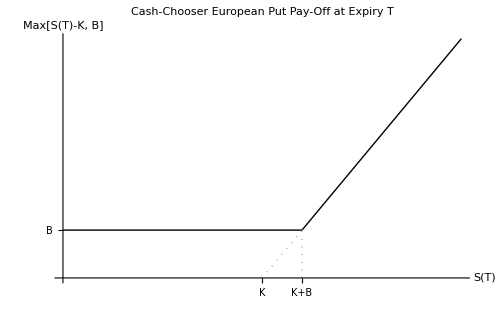

#### Example II — Comparing a Vanilla European Call and a Cash Chooser European Call

Consider a vanilla European call with the following parameters.

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 50., "Expiration"->0.25},  {"InterestRate"-> 0.1, "Volatility" -> 0.5,"CurrentPrice"->50.}]
```

5.55409

The value of a cash-chooser with the same parameters and cash payment of $10. is somewhat higher, reflecting the floor of B on the option at expiry.

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> (50.+10.), "Expiration"->0.25},  {"InterestRate"-> 0.1, "Volatility" -> 0.5,"CurrentPrice"->50.}]+ⅇ^(-0.1×0.25)10.
```

11.9181

### Chooser European Option

A standard chooser European option is one in which the option holder has the right to decide if the option is a put or a call at some point prior to the expiry of the option. We assume that the strike price K is the same both the put and call. To simplify the algebra assume the current time is 0, the time at which the choice must be made is τ, and the expiry is T with 0<τ<T.

F(0)=ⅇ^(-r τ)E_Q[max[C(τ|K,T),P(τ|K,T)]]

That is the current price of the chooser is the risk-neutral expected value of the maximum value of a put and a call at the choice point τ. Using put-call parity we replace P(τ|K,T)

F(0)=ⅇ^(-r τ)E_Q[max[C(τ|K,T),C(τ|K,T)-S(τ)+K ⅇ^(-r(T-τ))]]

Next we pull out C(τ|K,T) and rearrange terms

F(0)=ⅇ^(-r τ)E_Q[C(τ|K,T)]+ⅇ^(-r τ)E_Q[max[K ⅇ^(-r(T-τ))-S(τ), 0]]

F(0)=C(0|K,T)+P(0|K ⅇ^(-r(T-τ)),τ)

Thus, the chooser European option is a vanilla European call with strike K and expiry T and a vanilla European put with strike K ⅇ^(-r(T-τ)) and expiry τ.

For some general time 0≤t≤τ≤T we can obviously restate these results as

F(t)=C(t|K,T)+P(t|K ⅇ^(-r(T-τ)),τ)

#### Example I — Using Mathematica’s FinancialDerivative[] Function

First, we’ll solve for the price of a chooser using the solution we derived above. The chooser is at-the-money with parameters: K=50, τ=0.25, T=0.5, r=0.1, σ=0.5.

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 50., "Expiration"->0.5},  {"InterestRate"-> 0.1, "Volatility" -> 0.5,"CurrentPrice"->50.}]+FinancialDerivative[{"European","Put"}, {"StrikePrice"-> (50. ⅇ^(-0.1×(0.5-0.25))), "Expiration"->0.25},  {"InterestRate"-> 0.1, "Volatility" -> 0.5,"CurrentPrice"->50.}]
```

11.8611

The chooser European that is available in FinancialDerivative[] is more general, but for our case here (where the put and call have identical parameters) the parameters are set as below and the value is the same as the compound solution above.

```mathematica
FinancialDerivative[{"Chooser","European"},{"StrikePricePut"-> 50.,"StrikePriceCall"-> 50., "Expiration"->0.25,"ExpirationCall"->0.5,"ExpirationPut"->0.5},{"InterestRate"-> 0.1, "Volatility" -> 0.5,"CurrentPrice"->50.}]
```

11.8611

#### Example II — Plotting the Chooser

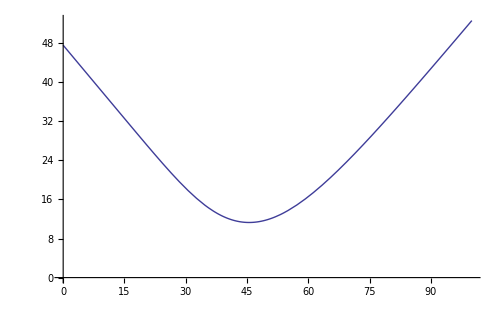

```mathematica
Plot[FinancialDerivative[{"Chooser","European"},{"StrikePricePut"-> 50.,"StrikePriceCall"-> 50., "Expiration"->0.25,"ExpirationCall"->0.5,"ExpirationPut"->0.5},{"InterestRate"-> 0.1, "Volatility" -> 0.5,"CurrentPrice"->p}],{p,0,100},AxesOrigin->{0,0},ImageSize->500]
```

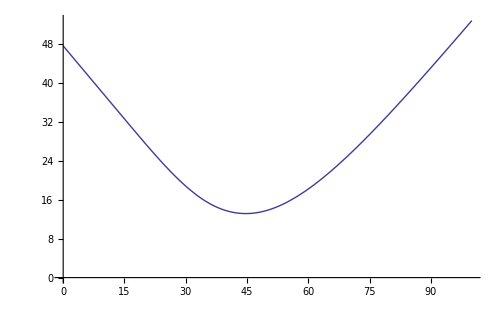

```mathematica
Plot[FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 50., "Expiration"->0.5},  {"InterestRate"-> 0.1, "Volatility" -> 0.5,"CurrentPrice"->p}]+FinancialDerivative[{"European","Put"}, {"StrikePrice"-> 50., "Expiration"->0.5},  {"InterestRate"-> 0.1, "Volatility" -> 0.5,"CurrentPrice"->p}],{p,0,100},AxesOrigin->{0,0},ImageSize->500]
```

## Monte Carlo Integration (Again) but with Dividends

Under the risk-neutral measure Q the price dynamics replaces the actual mean with the risk-free mean and keeps the same volatility. However, we saw that when there are cash-flows generated from the position at some proportional rate, then we must adjust the risk-free rate by subtracting the rate of cash-flows in and adding the rate of cash-flows out.

ⅆS(t)=(r-δ)S(t)ⅆt+σ S(t)ⅆW_Q(t)

ΔW_Q(t)\[Distributed]N[0,√Δ], S(0) known
ΔS(t+Δ)=(r-δ)S(t)Δ+σ S(t)ΔW_Q(t)
S(t+Δ)=S(t)+ΔS(t+Δ)

To price a call option we can generate n random samples. The Monte Carlo estimate for the integral is below. Note we have modified the rate in two places: in generating the price sample S^(k)(T) and in discounting e^(-(r-δ) T)E^Q[…]:

C(S(0),0)=e^(-(r-δ) T)E^Q[C(S(T),T)]≃e^(-(r-δ) T)(∑_(k=1)^n max[(S(0)ⅇ^(((r-δ)-σ^2/2)T+σ randN[0, √T]))-K, 0])/n

### Example I — European Call Option Pricing with Continuous Dividends

Applying standard statistical methodology we can compute the standard deviation of the estimate by dividing the standard deviation of the sample by square root of the sample size. A simulation with  n = 1000 is demonstrated. Consider the original Monte Carlo example: a call option at time t = 0 with a strike price K = 100 and expiry T = 0.25 years. The risk free rate is r = 6.5%. The underlying asset is currently at the money at S(0) = 100 and has an annual volatility of σ = 30%. We will now add the effect of a dividend rate δ=4%.

An at-the-money call is estimated at

```mathematica
xEuroCallOptMonteCarlo[100.,0.3,100.,0.25,0.065-0.04,1000]
```

{6.50814,0.302787}

{6.32741,0.313267}

{6.12133,0.293917}

{6.33829,0.300168}

For comparison, the Black-Scholes solution is

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 100.00, "Expiration"->0.25},  {"InterestRate"-> 0.065, "Dividend"->0.04,"Volatility" -> 0.3, "CurrentPrice"-> 100.}]
```

6.21414

### Example II — Plotting the Solution

We repeated this process for prices of 85 to 105. The results with ± 1.96 standard errors are plotted against the Black-Scholes results below.

#### Simulation of Estimates with their 95% Confidence Levels

```mathematica
mnSim=Transpose@Block[
{sol},
Table[
sol=xEuroCallOptMonteCarlo[price,0.3,100.,0.25,0.065-0.04,1000];
{{price,sol⟦1⟧-1.96sol⟦2⟧},{price,sol⟦1⟧},{price,sol⟦1⟧+1.96sol⟦2⟧}},
{price,85.,105.,5.}
]
]
```

{{{85.,0.847467},{90.,1.78061},{95.,3.31328},{100.,5.71291},{105.,8.85188}},{{85.,1.07779},{90.,2.12668},{95.,3.78917},{100.,6.32901},{105.,9.63086}},{{85.,1.30811},{90.,2.47275},{95.,4.26506},{100.,6.94511},{105.,10.4098}}}

#### Plot Comparing Black-Scholes and the Monte Carlo Solutions

A plot comparing the analytical Black-Scholes prices with the simulated prices and their 95% confidence intervals is

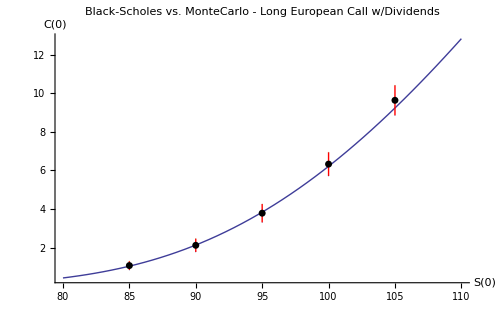

```mathematica
Show[
Plot[FinancialDerivative[{"European","Call"}, {"StrikePrice"-> 100.00, "Expiration"->0.25},  {"InterestRate"-> 0.065, "Dividend"->0.04,"Volatility" -> 0.3, "CurrentPrice"-> price}],{price,80,110},PlotLabel->Style["Black-Scholes vs. MonteCarlo - Long European Call w/Dividends",FontSize->16],AxesLabel->(Style[#,FontSize->14]&/@{"S(0)","C(0)"})],
ListPlot[mnSim,PlotStyle->{{PointSize[0]},{Black,PointSize[0.01]},{PointSize[0]}},Filling->{1->{3}},FillingStyle->Red],PlotRange->All,ImageSize->500
]
```

## Implied Volatility

Although we have presented methods for pricing options based on the descriptions of the option and underlying, in practice most options are traded in real markets and what we have is the market price of the option and must infer from that price  the underlying’s implied volatility. Implied volatility is also a useful surrogate for price in comparing different options on the same underlying in manner similar to way yield is used to compare like bonds of different maturities.

The table below represents data downloaded from Yahoo!Finance for the stock IBM and a few of the options available for it:

IBM
t = {2014,4,25} - S(t) = 189.63 - r = 0.007
Type | F(t) | K | T
Call | 6.25 | 185. | {2014,5,14}
Put | 0.13 | 170. | {2014,5,14}
Call | 5.75 | 190 | {2014,7,18}
Put | 13.5 | 200 | {2014,7,18}

We can use FinancialDerivative[] to solve for the implied volatilities for these options. These options are vanilla American options. The difference between a European and American option is that a European option is exercised at expiration and an American option can be exercised at any time up to an including expiration. Note that we do not include an ambient parameter for volatility and add a final argument identifying the desired computation.  Also, note that time parameters can be specified as dates and that we then must define a current time using the ambient parameter “ReferenceTime”.

```mathematica
FinancialDerivative[{"American","Call"},{"StrikePrice"->185,"Expiration"->{2014,5,14}},{"CurrentPrice"->189.63,"InterestRate"->0.007,"Value"->6.25,"ReferenceTime"->{2014,4,25}},"ImpliedVolatility"]
```

0.216024

```mathematica
FinancialDerivative[{"American","Put"},{"StrikePrice"->170,"Expiration"->{2014,5,14}},{"CurrentPrice"->189.63,"InterestRate"->0.007,"Value"->0.13,"ReferenceTime"->{2014,4,25}},"ImpliedVolatility"]
```

0.226829

```mathematica
FinancialDerivative[{"American","Call"},{"StrikePrice"->190,"Expiration"->{2014,7,18}},{"CurrentPrice"->189.63,"InterestRate"->0.007,"Value"->5.75,"ReferenceTime"->{2014,4,25}},"ImpliedVolatility"]
```

0.168276

```mathematica
FinancialDerivative[{"American","Put"},{"StrikePrice"->200,"Expiration"->{2014,7,18}},{"CurrentPrice"->189.63,"InterestRate"->0.007,"Value"->13.50,"ReferenceTime"->{2014,4,25}},"ImpliedVolatility"]
```

0.176313

Adding these results to our data gives

IBM
t = {2014,4,25} - S(t) = 189.63 - r = 0.007
Type | F(t) | K | T | σ (implied)
Call | 6.25 | 185. | {2014,5,14} | 0.21602
Put | 0.13 | 170. | {2014,5,14} | 0.22683
Call | 5.75 | 190 | {2014,7,18} | 0.16828
Put | 13.5 | 200 | {2014,7,18} | 0.17631

First, while options with corresponding expiries have volatilities which are close, they are not exactly the same. As the computation below show, if we use the volatility from the put to value the call, then the price increases from $6.25 to $6.40, a quite material difference. While there may be opportunities to profit from such differences across options, they are not nearly as large as they appear and may not exist at all. Many of the options are not very liquid with large bid-ask spreads. Attempting to set up apparent arbitrages will usually find any supposed profits swamped by costs and the uncertainties of execution.

```mathematica
FinancialDerivative[{"American","Call"},{"StrikePrice"->185,"Expiration"->{2014,5,14}},{"CurrentPrice"->189.63,"Volatility"->0.21602434537043813,"InterestRate"->0.007,"ReferenceTime"->{2014,4,25}}]
```

6.25

```mathematica
FinancialDerivative[{"American","Call"},{"StrikePrice"->185,"Expiration"->{2014,5,14}},{"CurrentPrice"->189.63,"Volatility"->0.22682868141195933,"InterestRate"->0.007,"ReferenceTime"->{2014,4,25}}]
```

6.39575

Second, as we can see the options expiring in July have lower volatilities than those in May. For vanilla American options increasing volatility results in increasing price; hence, in the sense of implied volatility, it appears that the July options are priced “cheaper” than the May options.

## Option "Greeks"

The option "Greeks" are a collection of partial derivatives of the option price with respect to a number of different parameters. Options are often used to hedge out various risks and so quantifying these relationships is important. We will derive results for European options.

Consider the option parameters as a vector of rules :

```mathematica
vrOptionParams={s->62,k->60,σ->0.2,r->0.1,t->5/12};
```

The Black-Scholes option pricing formulas for a call and a put expressed as "raw" expressions are

```mathematica
xCall=s (1+Erf[(Log[s/k]+(r+σ^2/2)t)/(σ √t)/√2])/2-k Exp[-r t](1+Erf[((Log[s/k]+(r+σ^2/2)t)/(σ √t)-σ √t)/√2])/2
```

1/2 s (1+Erf[(t (r+σ^2/2)+Log[s/k])/(√2 √t σ)])-1/2 ⅇ^(-r t) k (1+Erf[(-√t σ+(t (r+σ^2/2)+Log[s/k])/(√t σ))/(√2)])

```mathematica
xPut=xCall+Exp[-r t]k-s
```

ⅇ^(-r t) k-s+1/2 s (1+Erf[(t (r+σ^2/2)+Log[s/k])/(√2 √t σ)])-1/2 ⅇ^(-r t) k (1+Erf[(-√t σ+(t (r+σ^2/2)+Log[s/k])/(√t σ))/(√2)])

```mathematica
ReleaseHold[Hold[FinancialDerivative[{"European","Call"},{"StrikePrice"->k,"Expiration"->t},{"CurrentPrice"->s,"Volatility"->σ,"InterestRate"->r}]]/.vrOptionParams]
```

5.79778

```mathematica
xCall/.vrOptionParams
```

5.79778

```mathematica
ReleaseHold[Hold[FinancialDerivative[{"European","Put"},{"StrikePrice"->k,"Expiration"->t},{"CurrentPrice"->s,"Volatility"->σ,"InterestRate"->r}]]/.vrOptionParams]
```

1.34915

```mathematica
xPut/.vrOptionParams
```

1.34915

In what follows, when we discuss or contrast a put and call option we mean options on the same underlying with the same strike and expiry.

### Delta

Delta is the partial derivative of the option price with respect to the price of the underlying. This is also called the delta hedge ratio.

Δ=(∂F)/(∂S)

```mathematica
xDeltaCall=FullSimplify[D[xCall, s]]
xDeltaPut=FullSimplify[D[xPut, s]]
```

1/2 (1+Erf[(t (2 r+σ^2)+2 Log[s/k])/(2 √2 √t σ)])

-1/2 Erfc[(t (2 r+σ^2)+2 Log[s/k])/(2 √2 √t σ)]

Note, it is useful to recall in the following that Erfc[x] == (1 — Erf[x]). A little algebra is sufficient to show that the following relationship exists between the Deltas of a put and a call.

Δ_P=Δ_C-1

```mathematica
xDeltaPut/.vrOptionParams
(xDeltaCall-1)/.vrOptionParams
```

-0.260668

-0.260668

### Gamma

The Gamma is the second partial derivative of the option price with respect to the price of the underlying.

Γ=(∂^2 F)/(∂S^2)

```mathematica
xGammaCall=FullSimplify[D[xCall, s,s]]
```

(ⅇ^(-(t^2 (2 r+σ^2)^2+4 Log[s/k]^2)/(8 t σ^2)) k (s/k)^(1/2-r/σ^2))/(√(2 π) s^2 √t σ)

```mathematica
xGammaPut=FullSimplify[D[xPut, s,s]]
```

(ⅇ^(-(t^2 (2 r+σ^2)^2+4 Log[s/k]^2)/(8 t σ^2)) k (s/k)^(1/2-r/σ^2))/(√(2 π) s^2 √t σ)

As expected, the Gammas of a put and a call are the same.

Γ_P=Γ_C

```mathematica
xGammaPut/.vrOptionParams
xGammaCall/.vrOptionParams
```

0.0405782

0.0405782

### Theta

Theta is the partial derivative of the price of the option with respect to time. It is, all else held constant, the rate of decay in the option premium. It is sometimes called the "bleed".

Θ=(∂F)/(∂t)

```mathematica
xThetaCall=FullSimplify[D[xCall, t]]
```

1/4 ⅇ^(-r t) k (2 r+(ⅇ^(-(t^2 (-2 r+σ^2)^2+4 Log[s/k]^2)/(8 t σ^2)) √(2/π) (s/k)^(1/2-r/σ^2) σ)/(√t)+2 r Erf[(2 r t-t σ^2+2 Log[s/k])/(2 √2 √t σ)])

```mathematica
xThetaPut=FullSimplify[D[xPut, t]]
```

1/4 ⅇ^(-r t) k ((ⅇ^(-(t^2 (-2 r+σ^2)^2+4 Log[s/k]^2)/(8 t σ^2)) √(2/π) (s/k)^(1/2-r/σ^2) σ)/(√t)-2 r Erfc[(2 r t-t σ^2+2 Log[s/k])/(2 √2 √t σ)])

A little algebra suffices to show that

Θ_P=Θ_C-r K ⅇ^(-r T)

```mathematica
xThetaPut/.vrOptionParams
(xThetaCall-r k Exp[-r t])/.vrOptionParams
```

1.36859

1.36859

### Rho

Rho is the partial derivative of the option price with respect to the risk-free rate.

ρ=(∂F)/(∂r)

```mathematica
xRhoCall=FullSimplify[D[xCall, r]]
```

1/2 ⅇ^(-r t) k t (1+Erf[(2 r t-t σ^2+2 Log[s/k])/(2 √2 √t σ)])

```mathematica
xRhoPut=FullSimplify[D[xPut, r]]
```

-1/2 ⅇ^(-r t) k t Erfc[(2 r t-t σ^2+2 Log[s/k])/(2 √2 √t σ)]

Again, we have a relatively simple relationship between the Rho of a put and a call.

ρ_P=ρ_C-K T ⅇ^(-r T)

```mathematica
xRhoPut/.vrOptionParams
(xRhoCall-k t Exp[-r t])/.vrOptionParams
```

-7.29607

-7.29607

### Vega

Vega is the partial derivative of the option price with respect to the volatility of the underlying. The choice of the term Vega is strange but originated with Fischer Black and Myron Scholes themselves. Perhaps the "V" is suggestive of volatility?

𝒱=(∂F)/(∂σ)

```mathematica
xVegaCall=FullSimplify[D[xCall, σ]]
```

(ⅇ^(-(t^2 (2 r+σ^2)^2+4 Log[s/k]^2)/(8 t σ^2)) k (s/k)^(1/2-r/σ^2) √t)/(√(2 π))

```mathematica
xVegaPut=FullSimplify[D[xPut, σ]]
```

(ⅇ^(-(t^2 (2 r+σ^2)^2+4 Log[s/k]^2)/(8 t σ^2)) k (s/k)^(1/2-r/σ^2) √t)/(√(2 π))

We can see that the Vegas for a put and a call are identical.

𝒱_P=𝒱_C

```mathematica
xVegaPut/.vrOptionParams
xVegaCall/.vrOptionParams
```

12.9985

12.9985

### Delta Decay (Charm)

The Delta Decay (sometimes called Charm) is the second partial derivative of the option price with respect to the price of the underlying and time.

𝒞=(∂^2 F)/(∂S∂t)

```mathematica
xCharmCall=FullSimplify[D[xCall, s,t]]
```

(ⅇ^(-(t^2 (2 r+σ^2)^2+4 Log[s/k]^2)/(8 t σ^2)) (s/k)^(-1/2-r/σ^2) (t (2 r+σ^2)-2 Log[s/k]))/(4 √(2 π) t^(3/2) σ)

```mathematica
xCharmPut=FullSimplify[D[xPut, s,t]]
```

(ⅇ^(-(t^2 (2 r+σ^2)^2+4 Log[s/k]^2)/(8 t σ^2)) (s/k)^(-1/2-r/σ^2) (t (2 r+σ^2)-2 Log[s/k]))/(4 √(2 π) t^(3/2) σ)

The Charms of a put and a call are identical.

𝒞_P=𝒞_C

```mathematica
xCharmPut/.vrOptionParams
xCharmCall/.vrOptionParams
```

0.0519578

0.0519578

### Greek Functions

We have to force evaluation of the various Greek expressions in the following function definations. We also must be careful that we have not defined any values for our variables s, t, k, σ and r; otherwise, our expressions will evaluate to those specific values rather than keeping the formulae in symbolic form.

```mathematica
xCalcDeltaPut[s_,t_,k_,σ_,r_]:=Evaluate[xDeltaPut];
xCalcDeltaCall[s_,t_,k_,σ_,r_]:=Evaluate[xDeltaCall];
```

```mathematica
xCalcGamma[s_,t_,k_,σ_,r_]:=Evaluate[xGammaPut];
```

```mathematica
xCalcRhoPut[s_,t_,k_,σ_,r_]:=Evaluate[xRhoPut];
xCalcRhoCall[s_,t_,k_,σ_,r_]:=Evaluate[xRhoCall];
```

```mathematica
xCalcThetaPut[s_,t_,k_,σ_,r_]:=Evaluate[xThetaPut];
xCalcThetaCall[s_,t_,k_,σ_,r_]:=Evaluate[xThetaCall];
```

```mathematica
xCalcVega[s_,t_,k_,σ_,r_]:=Evaluate[xVegaCall];
```

```mathematica
xCalcCharm[s_,t_,k_,σ_,r_]:=Evaluate[xCharmCall];
```

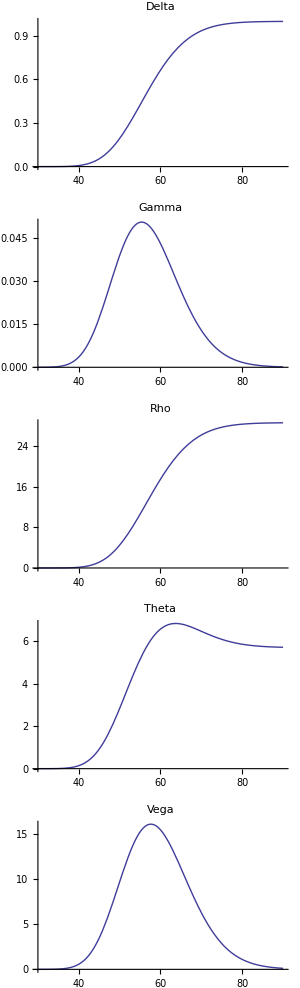

```mathematica
Show[
GraphicsGrid[{
{Plot[xCalcDeltaCall[s,0.5,60,0.2,0.1],{s,30,90},PlotLabel->"Delta"]},
{Plot[xCalcGamma[s,0.5,60,0.2,0.1],{s,30,90},PlotLabel->"Gamma"]},
{Plot[xCalcRhoCall[s,0.5,60,0.2,0.1],{s,30,90},PlotLabel->"Rho"]},
{Plot[xCalcThetaCall[s,0.5,60,0.2,0.1],{s,30,90},PlotLabel->"Theta"]},
{Plot[xCalcVega[s,0.5,60,0.2,0.1],{s,30,90},PlotLabel->"Vega"]}
}],
ImageSize->300
]
```

```mathematica
Plot3D[xCalcDeltaPut[s,t,60,0.2,0.1],{s,30,90},{t,0,1},PlotLabel->"Delta"]
```

-Graphics3D-

```mathematica
Plot3D[xCalcVega[s,t,60,0.2,0.1],{s,30,90},{t,0,1},PlotLabel->"Vega"]
```

-Graphics3D-

```mathematica
Plot3D[xCalcThetaCall[s,t,60,0.2,0.1],{s,30,90},{t,0,1},PlotLabel->"Theta"]
```

-Graphics3D-

### FinancialDerivative[]

FinancialDerivative[] is capable of computing many of the Greeks:

```mathematica
FinancialDerivative[{"European","Put"},{"StrikePrice"->60.,"Expiration"->5/12},{"CurrentPrice"->62.,"Volatility"->0.2,"InterestRate"->0.1},"Greeks"]
```

{Delta→-0.260668,Gamma→0.0405782,Rho→-7.29599,Theta→-1.36853,Vega→12.9986}

## Other Options

The options we have discussed so far have been, with a few exceptions, been vanilla European options. There is, however, a large number of other options which can be used as mechanisms for hedging risks. As can be seen from the listing below, we have barely scratched the surface. The basic tools of stochastic calculus and risk-neutral pricing that we have developed in this lecture are the foundations for the pricing of all of these derivatives. The various solution approaches: lattice models, PDEs, Monte Carlo simulation, finite difference methods, and forming portfolios of simpler instruments to replicate more complex ones are all part of the tool kit of financial engineers who build and price these instruments.

### FinancialDerivative[]

When FinancialDerivative[] is called without any arguments, it gives a list of all of the options types it is capable of pricing.

```mathematica
FinancialDerivative[]
```

{Altiplano,{American,Call},{American,Put},Annapurna,{AsianArithmetic,European,Call},{AsianArithmetic,European,Put},{AsianGeometric,European,Call},{AsianGeometric,European,Put},Atlas,{BarrierDownIn,American,Call},{BarrierDownIn,American,Put},{BarrierDownIn,European,Call},{BarrierDownIn,European,Put},{BarrierDownOut,American,Call},{BarrierDownOut,American,Put},{BarrierDownOut,European,Call},{BarrierDownOut,European,Put},{BarrierUpIn,American,Call},{BarrierUpIn,American,Put},{BarrierUpIn,European,Call},{BarrierUpIn,European,Put},{BarrierUpOut,American,Call},{BarrierUpOut,American,Put},{BarrierUpOut,European,Call},{BarrierUpOut,European,Put},{BinaryAsset,European,Call},{BinaryAsset,European,Put},{BinaryCash,European,Call},{BinaryCash,European,Put},{Chooser,European},{CompoundCall,European,Call},{CompoundCall,European,Put},{CompoundPut,European,Call},{CompoundPut,European,Put},{DoubleBarrierKnockIn,American,Call},{DoubleBarrierKnockIn,American,Put},{DoubleBarrierKnockIn,European,Call},{DoubleBarrierKnockIn,European,Put},{DoubleBarrierKnockOut,American,Call},{DoubleBarrierKnockOut,American,Put},{DoubleBarrierKnockOut,European,Call},{DoubleBarrierKnockOut,European,Put},{European,Call},{European,Put},Everest,{ExtendibleHolder,European,Call},{ExtendibleHolder,European,Put},{ExtendibleWriter,European,Call},{ExtendibleWriter,European,Put},{Future,European,Call},{Future,European,Put},Himalaya,{LookbackFixed,European,Call},{LookbackFixed,European,Put},{LookbackFloating,American,Call},{LookbackFloating,American,Put},{LookbackFloating,European,Call},{LookbackFloating,European,Put},{OneTouch,American,Call},{OneTouch,American,Put},{Perpetual,American,Call},{Perpetual,American,Put},{PerpetualLookback,Call},{PerpetualLookback,Put},{Power,European,Call},{Power,European,Put},{PowerCapped,European,Call},{PowerCapped,European,Put},{Powered,European,Call},{Powered,European,Put},{QuantoFixedExchange,American,Call},{QuantoFixedExchange,American,Put},{QuantoFixedExchange,European,Call},{QuantoFixedExchange,European,Put},{QuantoFixedStrike,American,Call},{QuantoFixedStrike,American,Put},{QuantoFixedStrike,European,Call},{QuantoFixedStrike,European,Put},{RainbowBest,American},{RainbowBest,European},{RainbowMax,American,Call},{RainbowMax,American,Put},{RainbowMax,European,Call},{RainbowMax,European,Put},{RainbowMin,American,Call},{RainbowMin,American,Put},{RainbowMin,European,Call},{RainbowMin,European,Put},{RainbowMoney,American},{RainbowMoney,European},{RainbowWorst,American},{RainbowWorst,European},Russian,{Spread,American,Call},{Spread,American,Put},{Spread,European,Call},{Spread,European,Put},{Vanilla,American,Call},{Vanilla,American,Put},{Vanilla,European,Call},{Vanilla,European,Put}}

If FinancialDerivative[] is called with an option name, then it will return the parameters and the minimum ambient parameters needed to price it.

```mathematica
FinancialDerivative[{"AsianGeometric","European","Call"}]
```

{{StrikePrice,Expiration,Inception,AverageSoFar},{CurrentPrice,Dividend,Volatility,InterestRate}}

```mathematica
FinancialDerivative[{"LookbackFloating","American","Put"}]
```

{{Expiration,MaxSoFar},{CurrentPrice,Dividend,Volatility,InterestRate}}

FinancialDerivative[] is also capable of producing more than a price, e.g.

```mathematica
FinancialDerivative[{"American","Put"},{"StrikePrice"->100.,"Expiration"->0.5},{"CurrentPrice"->98,"Volatility"->0.4,"InterestRate"->0.02},"Rules"]
```

{Value→11.541,Greeks→{Delta→-0.46169,Gamma→0.0148049,Rho→-23.9187,Theta→-10.1732,Vega→27.8244},CriticalValue→65.6566}

### American Options

Vanilla American options are the same as vanilla  European options with one change: the option may be exercised at any time up to and including expiry rather than just at expiry. An American option is an example of a path dependent option, because its value depends upon the path (affecting the exercise decision). In contrast, a European option is path independent.

Stock options are usually American options, while options on indexes are European. The pricing solution involves a backward dynamic program usually on a binomial lattice. Because of the additional flexibility offered, an American option's price is greater than or equal to that of a corresponding European option’s.

### LEAPS

LEAPS, or long-term equity anticipation securities, are exchange traded options with long expiries, e.g., up to 3 years.

### Exotic Options

There are a large class of options characterized as exotic. See http://en.wikipedia.org/wiki/Exotic_options and its associated links for more information. A few examples are:

#### Asian Options

In an Asian option the value depends on the average price of the option during the life of the option. There are two forms of the Asian. In one the strike price is the average price. In the other, the final value of the underlying is the average price.

#### Bermudian Options

Bermudian options have specific time points or time periods when the option may be exercised. Thus, a Bermudian option represents something between an American and European option.

#### Lookback Options

In one form of the lookback option the strike price floats and is based on the extreme value of the underlying during the period of the option. In a put, it is the maximum price, In a call, it is the minimum price. Lookback options with a floating strike can be priced with the Black-Scholes, although the computations are more complicated. In another form of the lookback the final price floats In a put it is based on the minimum and a call on the maximum.

#### Knockout Options

A knockout option is a form of barrier option and terminates with 0 value if the price of the underlying reaches a specified value. For a put, the option is “up and out” where the option terminates if the underlying’s price exceeds a threshold value. For a call, the option is “down and out” where the option terminates if the underlying’s price falls below a threshold value. In another form of barrier option, the option does not activate until after the price crosses a defined threshold.